## Chapter 10: Neural Networks Framework

## 10.1 Gradient Descent Algorithm

### 10.1.1 Training a Neural Network

### 10.1.2 Data Input

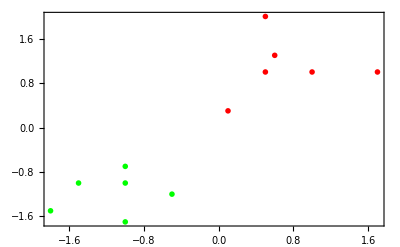

```mathematica
plt=ListPlot[{{{-1.8,-1.5},{-1,-1.7},{-1.5,-1},{-1,-1},{-0.5,-1.2},{-1,-0.7}},{{1,1},{1.7,1},{0.5,2},{0.1,0.3},{0.5,1},{0.6,1.3}}},PlotMarkers->"OpenMarkers",Frame->True,PlotStyle->{Green,Red}]
```

```mathematica
data={{-1.8,-1.5},{-1,-1.7},{-1.5,-1},{-1,-1},{-0.5,-1.2},{-1,-0.7},{1,1},{1.7,1},{0.5,2},{0.1,0.3},{0.5,1},{0.6,1.3}};
target={-1,-1,-1,-1,-1,-1,1,1,1,1,1,1};
trainData=MapThread[#1->{#2}&,{Standardize[data],target},1];
```

```mathematica
model=NetChain[{LinearLayer[1,"Input"->2],ElementwiseLayer[Ramp[#]&]}];
```

### 10.1.3 Training Phase

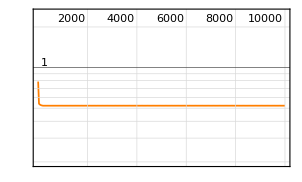
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:18s  examples/s:6671
data | ,,  training examples:12  processed examples:120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size12CPU
round | ,,  loss:5.22×10^-1
 | rounds
loss | -Graphics- | 
 | ]

```mathematica
net=NetTrain[model,trainData,All,LearningRate->0.01,PerformanceGoal->"TrainingSpeed",TrainingProgressReporting->"Panel",TargetDevice->"CPU",RandomSeeding->88888,WorkingPrecision->"Real64"]
```

### 10.1.4 Model Implementation

```mathematica
trainedNet1=net["TrainedNet"]
```

NetChain[…]

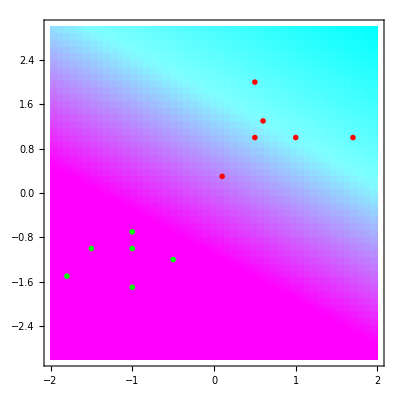

```mathematica
Show[DensityPlot[trainedNet1[{x,y}],{x,-2,2},{y,-3,3},PlotPoints->50,ColorFunction->(RGBColor[1-#,2*#,1]&)],Plt]
```

### 10.1.5 Batch Size and Rounds

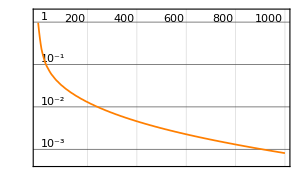
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3000  rounds:1000  time:4.9s  examples/s:3091
data | ,,  training examples:12  processed examples:15000  skipped examples:0
method | ,,  ADAMoptimizer  batch size5CPU
round | ,,  loss:8.12×10^-4
 | rounds
loss | -Graphics- | 
 | ]

```mathematica
net2=NetTrain[NetChain[{LinearLayer[1,"Input"->2],ElementwiseLayer[Tanh[#]&]}],trainData,All,LearningRate->0.01,PerformanceGoal->"TrainingSpeed",TrainingProgressReporting->"Panel",TargetDevice->"CPU",RandomSeeding->88888,WorkingPrecision->"Real64",LossFunction->MeanSquaredLossLayer[],BatchSize->5,MaxTrainingRounds->1000]
```

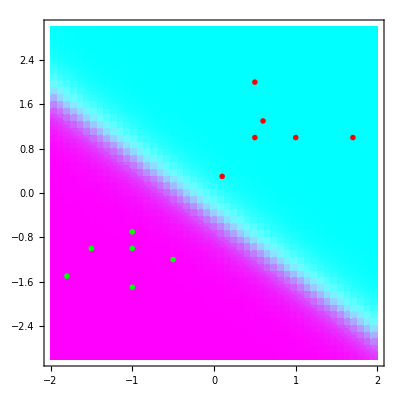

```mathematica
trainedNet2=net2["TrainedNet"];
Show[DensityPlot[trainedNet2[{x,y}],{x,-2,2},{y,-3,3},PlotPoints->50,ColorFunction->(RGBColor[1-#,2*#,1]&)],Plt]
```

```mathematica
Dataset[{Association["LossPlot"->net2["LossPlot"]],Association["NetGraph"->net2["TrainingNet"]]}]
```

```mathematica
net2["TrainingNet"]
```

NetGraph[…]

```mathematica
net2["Properties"]
```

{ArraysLearningRateMultipliers,BatchesPerRound,BatchesPerSecond,BatchLossList,BatchMeasurements,BatchMeasurementsLists,BatchSize,BestValidationRound,CheckpointingFiles,ExamplesProcessed,FinalLearningRate,FinalPlots,InitialLearningRate,InternalVersionNumber,LossPlot,MeanBatchesPerSecond,MeanExamplesPerSecond,NetTrainInputForm,OptimizationMethod,ReasonTrainingStopped,RoundLoss,RoundLossList,RoundMeasurements,RoundMeasurementsLists,RoundPositions,SkippedTrainingData,TargetDevice,TotalBatches,TotalRounds,TotalTrainingTime,TrainedNet,TrainingExamples,TrainingNet,TrainingUpdateSchedule,ValidationExamples,ValidationLoss,ValidationLossList,ValidationMeasurements,ValidationMeasurementsLists,ValidationPositions}

### 10.1.6 Training Method

```mathematica
net2["OptimizationMethod"]
```

{ADAM,Beta1→0.9,Beta2→0.999,Epsilon→1/100000,GradientClipping→None,L2Regularization→None,LearningRate→0.01,LearningRateSchedule→None,WeightClipping→None}

### 10.1.7 Method Performance

```mathematica
net3=NetTrain[NetChain[{LinearLayer[1,"Input"->2],ElementwiseLayer["SoftSign"]}],trainData,All,LearningRate->0.01,PerformanceGoal->"TrainingSpeed",TrainingProgressReporting->"Panel",TargetDevice->"CPU",RandomSeeding->88888,WorkingPrecision->"Real64",Method->"ADAM",LossFunction->MeanSquaredLossLayer[],BatchSize->5,MaxTrainingRounds->1000,TrainingProgressMeasurements->{"MeanDeviation","MeanSquare","RSquared","StandardDeviation"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3000  rounds:1000  time:7.5s  examples/s:1992
data | ,,  training examples:12  processed examples:15000  skipped examples:0
method | ,,  ADAMoptimizer  batch size5CPU
round | ,,  loss:2.25×10^-2  res. mean dev.:1.42×10^-1  res. mean sqr.:2.25×10^-2  res. r.b2:9.77×10^-1  res. s.d.:1.5×10^-1
 | 
 | ]

### 10.1.8 Model Assessment

```mathematica
net3[#]&/@{"RoundMeasurements"}//Dataset[#]&
```

```mathematica
net3["FinalPlots"]//Dataset;
```

```mathematica
measures=net3[#]&/@{"RoundMeasurementsLists"};
Keys[measures]
```

{{Loss,MeanDeviation,MeanSquare,RSquared,StandardDeviation}}

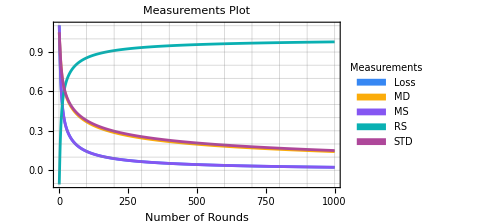
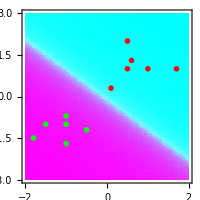
-Graphics- | -Graphics-

```mathematica
yrainedNet3=net3["TrainedNet"];Grid[{{ListLinePlot[{measures[[1,1]](*Loss*),measures[[1,2]] (*MeanDeviation*),measures[[1,3]](*MeanSquare*),measures[[1,4]] (*RSquared*),measures[[1,5]](*StandardDeviation*)},PlotStyle->Table[ColorData[101,i],{i,1,5}],Frame->True,FrameLabel->{"Number of Rounds",None},PlotLabel->"Measurements Plot",GridLines->All,PlotLegends->SwatchLegend[{Style["Loss",#],Style["MD",#],Style["MS",#],Style["RS",#],Style["STD",#]},LegendLabel->Style["Measurements",#],LegendFunction->(Framed[#,RoundingRadius->5,Background->LightGray]&)],ImageSize->Medium]&[Black],Show[DensityPlot[trainedNet3[{x,y}],{x,-2,2},{y,-3,3},PlotPoints->50,ColorFunction->(RGBColor[1-#,2*#,1]&)],plt,ImageSize->200]}}]
```

### 10.1.9 Exporting a Neural Network

```mathematica
Export["/Users/macosx/Desktop/TrainedNet3.wlnet",net3["TrainedNet"]]
```

/Users/macosx/Desktop/TrainedNet3.wlnet

```mathematica
Dataset@AssociationMap[Import["/Users/macosx/Desktop/TrainedNet3.wlnet",#]&,{"Net","UninitializedNet","ArrayList","ArrayAssociation","WLVersion"}]
```

## 10.2 Wolfram Neural Net Repository

### 10.2.1 Selecting a Neural Net Model

```mathematica
ResourceSearch[{"Name"->"Image","ResourceType"->"NeuralNet"}]//Dataset[#,MaxItems->{4,3}]&
```

### 10.2.2 Accessing Inside Mathematica

```mathematica
ResourceSearch[{"Name"->"Wolfram ImageIdentify","ResourceType"->"NeuralNet"},"Object"]
```

{ResourceObject[…]}

```mathematica
ResourceSearch[{"Name"->"Wolfram ImageIdentify","ResourceType"->"NeuralNet"},"Object"][[1]]//ResourceData;
```

NetChain[<24>]

### 10.2.3 Retrieving Relevant Information

```mathematica
Dataset[AssociationMap[ResourceObject["Wolfram ImageIdentify Net V1"],{"Name","RepositoryLocation","ResourceType","ContentElements","Version","Description","TrainingSetInformation","InputDomains","TaskType","Keywords","Attributes","LatestUpdate","DownloadedVersion","Format","ContributorInformation","DOI","Originator","ReleaseDate","ShortName","WolframLanguageVersionRequired"}]]
```

## 10.3 LeNet Neural Network

### 10.3.1 LeNet Model

```mathematica
NetModel["LeNet Trained on MNIST Data",#]&/@{"Details","ShortName","TaskType","SourceMetadata"}//Column
```

This pioneer work for image classification with convolutional neural nets was released in 1998. It was developed by Yann LeCun and his collaborators at AT&T Labs while they experimented with a large range of machine learning solutions for classification on the MNIST dataset.
LeNet-Trained-on-MNIST-Data
{Classification}
<|Citation→Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998),Source→http://yann.lecun.com/exdb/lenet,Date→DateObject[{1998},Year,Gregorian,-5.]|>

```mathematica
NetModel["LeNet Trained on MNIST Data",#]&/@{"TrainingSetInformation","InputDomains","Performance"}//Column
```

MNIST Database of Handwritten Digits, consisting of 60,000 training and 10,000 test grayscale images of size 28x28.
{Image}
This model achieves 98.5% accuracy on the MNIST dataset.

### 10.3.2 MNIST Dataset

```mathematica
(*This is for seven elements randomly sampled,but you can check the whole data set.*)
TableForm[
SeedRandom[900];
RandomSample[ResourceData["MNIST","TrainingData"],7],TableDirections->Row]
Map[ImageDimensions,%[[1;;7,1]]](*Test set : ResourceData["MNIST","TestData"] *)
```

-Graphics-→9 | -Graphics-→5 | -Graphics-→2 | -Graphics-→2 | -Graphics-→6 | -Graphics-→0 | -Graphics-→7

{{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28}}

```mathematica
{trainData,testData}={ResourceData["MNIST","TrainingData"], ResourceData["MNIST","TestData"] };
```

### 10.3.3 LeNet Architecture

```mathematica
uninitLeNet=NetModel["LeNet Trained on MNIST Data","UninitializedEvaluationNet"](*To work locally with the untrained model: NetModel["LeNet"]*)
```

NetChain[…]

### 10.3.4 MXNet Framework

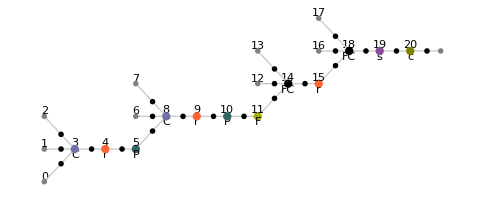

```mathematica
Information[uninitLeNet,"MXNetNodeGraphPlot"]
```

### 10.3.5 Preparing LeNet

```mathematica
NetGraph[uninitLeNet]
```

NetGraph[…]

```mathematica
{enc=NetExtract[uninitLeNet,"Input"],dec=NetExtract[uninitLeNet,"Output"]}//Row;
```

```mathematica
testNet=NetInitialize[uninitLeNet,RandomSeeding->8888];
testNet@trainData[[1,1]](*TrainData[[1,1]] belongs to a zero*)
```

9

```mathematica
{net1,net2,net3,net4}=Table[NetInitialize[uninitLeNet,All,Method->i,RandomSeeding->8888],{i,{"Kaiming","Xavier","Orthogonal","Identity"}}];
{net1[trainData[[1,1]]],net2[trainData[[1,1]]],net3[trainData[[1,1]]],net4[trainData[[1,1]]]}
```

{9,9,7,3}

```mathematica
leNet=NetInitialize[NetGraph[<|"LeNet NN"->uninitLeNet,"LeNet Loss"->CrossEntropyLossLayer@"Index"|>,{NetPort@"Input"->"LeNet NN","LeNet NN"->NetPort@{"LeNet Loss","Input"},NetPort@"Target"->NetPort@{"LeNet Loss","Target"}}],RandomSeeding->8888]
```

NetGraph[<2>, <4>]

```mathematica
trainDts=Dataset@Join[AssociationThread["Input"->#]& /@Keys[trainData],AssociationThread["Target"-> #]&/@Values[trainData]+1,2];
testDts=Dataset@Join[AssociationThread["Input"->#]& /@Keys[testData],AssociationThread["Target"-> #]&/@Values[testData]+1,2];
```

```mathematica
BlockRandom[SeedRandom[999];
{RandomSample[trainDts[[All]],4],RandomSample[testDts[[All]],4]}]
```

{,}

### 10.3.6 LeNet Training

```mathematica
netResults=NetTrain[leNet,trainDts,All,ValidationSet->testDts,MaxTrainingRounds->15,BatchSize->2096,LearningRate->Automatic,Method->"ADAM",TargetDevice->"CPU",PerformanceGoal->"TrainingMemory",WorkingPrecision->"Real32",RandomSeeding->99999,TrainingProgressMeasurements->{<|"Measurement"->"Accuracy","ClassAveraging"->"Macro"|>,
<|"Measurement"->"Precision","ClassAveraging"->"Macro"|>
,<|"Measurement"->"F1Score","ClassAveraging"->"Macro"|>
,<|"Measurement"->"Recall","ClassAveraging"->"Macro"|>
,<|"Measurement"->"ROCCurvePlot","ClassAveraging"->"Macro"|>
,<|"Measurement"->"ConfusionMatrixPlot","ClassAveraging"->"Macro"|>
},TrainingStoppingCriterion-> <|"Criterion"->"Loss","AbsoluteChange"->0.001|>]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:406  rounds:14  time:17min  examples/s:838
data | ,,  training examples:60000  validation examples:10000  processed examples:850976  skipped examples:0
method | ,,  ADAMoptimizer  batch size2096CPU
round | ,,  loss:2.67×10^-2  acc.:99.220%  prec.:99.215%  F1:99.214%  recall:99.213%
validation | ,,  loss:3.43×10^-2  acc.:98.85%  prec.:98.85%  F1:98.84%  recall:98.84%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
NetExtract[netResults["TrainedNet"],"LeNet NN"];
trainedLeNet=NetReplacePart[%,{"Input"->enc,"Output"->dec}];
```

### 10.3.7 LeNet Model Assessment

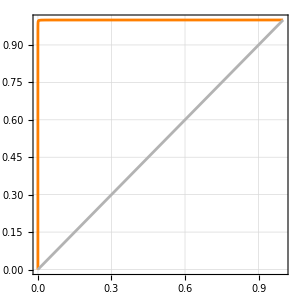
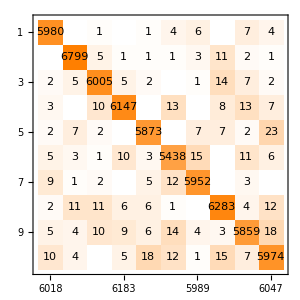
RoundMeasurements | ROCCurvePlot | ConfusionMatrixPlot
 | recall | -Graphics-
 | false positive rate | actual class | -Graphics-
 | predicted class

```mathematica
netResults["RoundMeasurements"][[1;;5]];
Normal[netResults["RoundMeasurements"][[6;;7]]];
Grid[{{Style["RoundMeasurements",#1,#2],Style[%[[1,1]],#1,#2],Style[%[[2,1]],#1,#2]},{Dataset[%%],%[[1,2]],%[[2,2]]}},Dividers->Center]&[Bold,FontFamily->"Alegreya SC"]
```

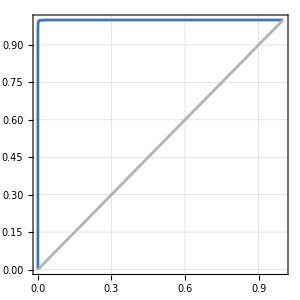
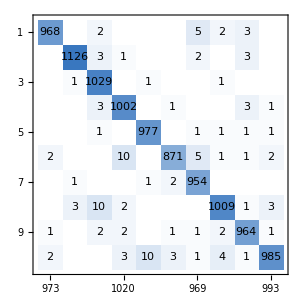
ValidationMeasurements | ROCCurvePlot | ConfusionMatrixPlot
 | recall | -Graphics-
 | false positive rate | actual class | -Graphics-
 | predicted class

```mathematica
netResults["ValidationMeasurements"][[1;;5]];
Normal[netResults["ValidationMeasurements"][[6;;7]]];
Grid[{{Style["ValidationMeasurements",#1,#2],Style[%[[1,1]],#1,#2],Style[%[[2,1]],#1,#2]},{Dataset[%%],%[[1,2]],%[[2,2]]}},Dividers->Center]&[Bold,FontFamily->"Alegreya SC"]
```

### 10.3.8 Testing LeNet

```mathematica
expls=Keys[{testData[[2150]],testData[[3910]],testData[[6115]],testData[[6011]],testData[[7834]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
trainedLeNet[expls,"TopProbabilities"]
```

{{2→0.999397},{3→0.999856},{6→0.906024},{6→0.990975},{7→0.999853}}

```mathematica
TableForm[Transpose@{trainedLeNet[expls,{"TopDecisions",2}],trainedLeNet[ expls,{"TopProbabilities",2}]},TableHeadings->{Map[ToString,{2,3,6,5,7},1],{"Top Decisions","Top Probabilities "}},TableAlignments->Center]
```

| Top Decisions | Top Probabilities 
2 | 3
2 | 3→0.000580186
2→0.999397
3 | 9
3 | 9→0.0000792077
3→0.999856
6 | 0
6 | 0→0.0904324
6→0.906024
5 | 5
6 | 5→0.00699159
6→0.990975
7 | 3
7 | 3→0.000104
7→0.999853

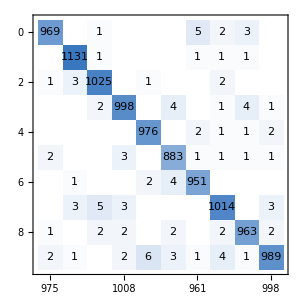
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[trainedLeNet,testData,"ConfusionMatrixPlot"]
```

## 10.4 Basics of GPT and LLM

### 10.4.1 Basic Overview of GPT and LLM

### 10.4.2 Overview of LLM in Wolfram Language

### 10.4.3 Chat Notebooks

```mathematica
Print["Hello World!"]
```

Hello World!

I need a brief and concise "Hello World!" example code with a two-sentence explanation.

To create a "Hello World!" example in Wolfram Language, you can use the following code snippet: 

When you evaluate this code, it will output "Hello World!" in the Wolfram Language environment. The Printpaclet:ref/Print function is commonly used to display messages or output in the notebook interface.

I need a brief and concise "Hello World!" example code with a two-sentence explanation.

This Python code uses the print function to display the text "Hello World!" on the screen. It is a common introductory program used to demonstrate the basic syntax of a programming language.

I need a brief and concise "Hello World!" example code with a two-sentence explanation.

This Python code uses the print function to output the phrase "Hello World!" to the console, which is a common first program when learning a new programming language.

### 10.4.4 Wolfram Prompt Repository

For[i = 1, i <= 5, i++, Print[i]]

Beep boop beep boop beep,
Loop and print numbers in code,
Haiku for the loop.

### 10.4.5 LLM Functionalities

```mathematica
ChatEvaluate[ChatObject[], "Break down this code in 3 simple points? For[i=1,i<=5,i++,Print[i]",LLMEvaluator-><|"Prompts"->{LLMPrompt["ELI5"]}|>] (*Explain Like I'm Five*)
```

ChatObject[…]

```mathematica
%["Messages"]
%%["Usage"]
```

{<|Role→User,Content→Answer questions as if the listener is a five year old child.

Break down this code in 3 simple points? For[i=1,i<=5,i++,Print[i],Timestamp→Thu 22 Feb 2024 11:22:05GMT-6,Annotations→<|{1,129}→Prompt|>|>,<|Role→Assistant,Content→1. This code is telling the computer to count from 1 to 5.
2. It is using the "for" loop to make this happen.
3. Every time it counts a number, it will print that number on the screen.,Timestamp→Thu 22 Feb 2024 11:22:06GMT-6,Annotations→<|{1,184}→Completion|>|>}

92 tokens

```mathematica
llmConfig=LLMConfiguration[<|"Prompts"->LLMPrompt["ELI5"],"Model"->"GPT-3.5-Turbo","Temperature"->0.1,"MaxTokens"->5|>];
LLMSynthesize["Break down this code in 3 simple points? For[i=1,i<=5,i++,Print[i]",LLMEvaluator->llmConfig]
```

Sure! Here's a

```mathematica
$LLMEvaluator=LLMConfiguration[<|"Prompts"->LLMPrompt["ELI5"],"Model"->"GPT-3.5-Turbo","Temperature"->0.1,"MaxTokens"->5|>]
```

LLMConfiguration[…]

### 10.4.6 GTP-1 and GPT-2 Models

```mathematica
Row[{Short[NetModel["GPT Transformer Trained on BookCorpus Data",#]&/@{"Details","ShortName"}//Column,4],Short[NetModel["GPT2 Transformer Trained on WebText Data",#]&/@{"Details","ShortName"}//Column,4]}]
```

Released in 2018, this Generative Pre-Training Transformer (GPT) model is pre-trained in an unsupervised fashion on a large corpus of English text. This model can be further fine-tuned with additional output layers to create highly accurate NLP models for a wide range of tasks. It uses bi-directional causal self-attention, often referred to as a transformer decoder.
GPT-Transformer-Trained-on-BookCorpus-DataReleased in 2019, this model improves and scales up its predecessor model. It has a richer vocabulary and uses BPE tokenization on UTF-8 byte sequences and additional normalization at the end of all of the transformer blocks.
GPT2-Transformer-Trained-on-WebText-Data

```mathematica
NetModel["GPT Transformer Trained on BookCorpus Data",#]&/@{"ParametersAllowedValues","Variants"}
NetModel["GPT2 Transformer Trained on WebText Data",#]&/@{"ParametersAllowedValues","Variants"}
```

{<|Task→{FeatureExtraction,LanguageModeling}|>,{{GPT Transformer Trained on BookCorpus Data,Task→FeatureExtraction},{GPT Transformer Trained on BookCorpus Data,Task→LanguageModeling}}}

{<|Task→{FeatureExtraction,LanguageModeling},Size→{117M,345M,774M}|>,{{GPT2 Transformer Trained on WebText Data,Task→FeatureExtraction,Size→117M},{GPT2 Transformer Trained on WebText Data,Task→FeatureExtraction,Size→345M},{GPT2 Transformer Trained on WebText Data,Task→FeatureExtraction,Size→774M},{GPT2 Transformer Trained on WebText Data,Task→LanguageModeling,Size→117M},{GPT2 Transformer Trained on WebText Data,Task→LanguageModeling,Size→345M},{GPT2 Transformer Trained on WebText Data,Task→LanguageModeling,Size→774M}}}

```mathematica
gpt1=NetModel[{"GPT Transformer Trained on BookCorpus Data","Task"-> "LanguageModeling"}]
gpt2=NetModel[{"GPT2 Transformer Trained on WebText Data","Task"-> "LanguageModeling"}]
```

NetChain[<5>]

NetChain[<5>]

```mathematica
generateText[LLmodel_][initialText_,tokenCount_:10,temperature_:1]:=Fold[StringJoin[#1,LLmodel[#1,{"RandomSample","Temperature"->temperature}]]&,initialText,Range[tokenCount]]
```

```mathematica
generateText[gpt1]["Alan Turing was a British mathematician and logician who is considered a pioneer in the field of computer science.",20,0.5]
```

Alan Turing was a British mathematician and logician who is considered a pioneer in the field of computer science.he is a physicist and is a very good scientist . 
 he is also a friend of george w.

```mathematica
generateText[gpt2]["Alan Turing was a British mathematician and logician who is considered a pioneer in the field of computer science.",20,1]
```

Alan Turing was a British mathematician and logician who is considered a pioneer in the field of computer science. At the time of his independence he was selected to pen one of the first (173) contributions to